```mathematica
SpecialPolygon[p_Integer]:=
Module[{iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,evencount=0,oddcount=0,pm4,pm3},
iterateMax=p^2;
t=Floor[Sqrt[p]];

pm3=Mod[p,3];
pm4=Mod[p,4];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
(*Print["iterate = ",iterate," and vb = ",vb];*)
For[j=1,j<Length[vw],j++,
(*Print["j is ",j," and vb is ",vb];   *)
If[vb[[j]]!=-4,Continue[]];
(* Only if p is 1 mod 4 *)
If[evencount<2&&pm4==1,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-2];evencount++;Continue[]]];
(* Only if p is 1 mod 3 *)
If[oddcount<2&&pm3==1,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-3];oddcount++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],p]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
 (*Print["Complete at p = ",p];*)
If[iterate==1,
(*Print["Compact at p = ",p];*)
cpt=True];
Break[]];
mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{cpt,vw,vb}];
];
```

```mathematica
SpecialPolygonZero[p_Integer]:=
Module[{iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,evencount=0,oddcount=0,pm4,pm3},
iterateMax=Floor[(p+1)/3];
t=2;

pm3=Mod[p,3];
pm4=Mod[p,4];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
(*Print["iterate = ",iterate," and vb = ",vb];*)
For[j=1,j<Length[vw],j++,
(*Print["j is ",j," and vb is ",vb];   *)
If[vb[[j]]!=-4,Continue[]];
(* Only if p is 1 mod 4 *)
If[evencount<2&&pm4==1,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-2];evencount++;Continue[]]];
(* Only if p is 1 mod 3 *)
If[oddcount<2&&pm3==1,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-3];oddcount++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],p]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
 (*Print["Complete at p = ",p];*)
If[iterate==1,
(*Print["Compact at p = ",p];*)
cpt=True];
Break[]];
mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{cpt,vw,vb}];
];
```

```mathematica
SpecialPolygonRandom[p_Integer]:=
Module[{iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,evencount=0,oddcount=0,pm4,pm3},
iterateMax=Floor[(p+1)/3];
t=2;

pm3=Mod[p,3];
pm4=Mod[p,4];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
(*Print["iterate = ",iterate," and vb = ",vb];*)
For[j=1,j<Length[vw],j++,
(*Print["j is ",j," and vb is ",vb];   *)
If[vb[[j]]!=-4,Continue[]];
(* Only if p is 1 mod 4 *)
If[evencount<2&&pm4==1,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-2];evencount++;Continue[]]];
(* Only if p is 1 mod 3 *)
If[oddcount<2&&pm3==1,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-3];oddcount++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],p]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
 (*Print["Complete at p = ",p];*)
If[iterate==1,
(*Print["Compact at p = ",p];*)
cpt=True];
Break[]];
(*mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];*)
mpos=RandomInteger[{1,Length[unclaimed]}];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{cpt,vw,vb}];
];
```

```mathematica
SpecialPolygonSqrtStart[p_Integer]:=
Module[{iterateMax,iterate,vw,vb,k,Found,unclaimed,mpos,m,j,j1,res,m1,cpt=False,evencount=0,oddcount=0,pm4,pm3},
iterateMax=Floor[(p+1)/3];
t=Floor[Sqrt[p]];

pm3=Mod[p,3];
pm4=Mod[p,4];

vw=Denominator[FareySequence[t]];
vb=Table[-4,Length[vw]-1];


k=0;
Found=False;
For[iterate=1,iterate<=iterateMax&&!Found,iterate++,
(*Print["iterate = ",iterate," and vb = ",vb];*)
For[j=1,j<Length[vw],j++,
(*Print["j is ",j," and vb is ",vb];   *)
If[vb[[j]]!=-4,Continue[]];
(* Only if p is 1 mod 4 *)
If[evencount<2&&pm4==1,
If[Mod[vw[[j]]^2+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-2];evencount++;Continue[]]];
(* Only if p is 1 mod 3 *)
If[oddcount<2&&pm3==1,
If[Mod[vw[[j]]^2+vw[[j]]vw[[j+1]]+vw[[j+1]]^2,p]==0,vb=ReplacePart[vb,j->-3];oddcount++;Continue[]]];
For[j1=j+1,j1<Length[vw],j1++,
If[vb[[j1]]==-4&&Mod[vw[[j]]vw[[j1]]+vw[[j+1]]vw[[j1+1]],p]==0,vb=ReplacePart[vb,j->++k];
vb=ReplacePart[vb,j1->k];Continue[]]];
];

unclaimed=Flatten[Position[vb,-4]];
(* If no black vertices are labeled -4, then our computation is complete and safe *)

If[unclaimed=={},
Found=True;res=Max[vw];
 (*Print["Complete at p = ",p];*)
If[iterate==1,
(*Print["Compact at p = ",p];*)
cpt=True];
Break[]];
mpos=1;
m=Plus[vw[[unclaimed[[1]]]],vw[[unclaimed[[1]]+1]]];
For[j=2,j<=Length[unclaimed],j++,
m1=Plus[vw[[unclaimed[[j]]]],vw[[unclaimed[[j]]+1]]];
If[m>m1,mpos=j;m=m1;
];
];
j=unclaimed[[mpos]];
vw = Insert[vw,vw[[j]]+vw[[j+1]],j+1];
vb=Insert[vb,-4,j+1];
];
Return[{cpt,vw,vb}];
];
```

```mathematica
l101103={1,103,102,101,100,99,98,97,96,95,94,93,92,91,90,89,88,87,86,85,84,83,82,81,80,79,78,77,76,75,74,73,72,71,70,69,68,67,66,65,64,63,62,61,60,59,58,57,56,111,55,54,107,53,105,52,103,51,101,50,99,49,97,48,95,47,93,46,91,45,89,44,87,43,85,42,83,41,81,40,79,39,77,38,75,112,37,73,36,107,71,106,35,104,69,103,34,101,67,100,33,98,65,97,32,95,63,94,31,92,61,91,30,89,59,88,29,86,57,85,28,83,55,82,109,27,80,53,79,105,26,103,77,51,76,101,25,99,74,49,73,97,24,95,71,47,70,93,23,91,68,45,112,67,89,22,109,87,65,108,43,64,85,106,21,104,83,62,103,41,102,61,81,101,20,99,79,59,98,39,97,58,77,96,19,94,75,56,93,37,92,55,73,91,18,107,89,71,53,88,35,87,52,69,86,103,17,101,84,67,50,83,33,82,49,65,81,97,16,95,79,63,47,78,31,108,77,46,107,61,76,91,15,104,89,74,59,103,44,73,102,29,101,72,43,100,57,71,85,99,14,97,83,69,55,96,41,109,68,95,27,94,67,107,40,93,53,66,79,92,105,13,103,90,77,64,51,89,38,101,63,88,25,87,62,99,37,86,49,61,73,85,97,12,95,83,71,59,106,47,82,35,93,58,81,104,23,103,80,57,91,34,79,45,101,56,67,78,89,100,11,98,87,76,65,54,97,43,75,32,85,53,74,95,21,94,73,52,83,31,103,72,113,41,92,51,61,71,81,91,101,10,99,89,79,69,59,108,49,88,39,107,68,97,29,106,77,48,67,86,105,19,104,85,66,47,75,103,28,93,65,102,37,83,46,101,55,64,73,82,91,100,9,98,89,80,71,62,53,97,44,79,35,96,61,87,26,95,69,112,43,103,60,77,94,17,93,76,59,101,42,67,92,25,108,83,58,91,33,74,41,90,49,106,57,65,73,81,89,97,8,103,95,87,79,71,63,55,102,47,86,39,70,101,31,85,54,77,100,23,107,84,61,99,38,91,53,68,83,98,15,97,82,67,52,89,37,96,59,81,103,22,95,73,51,80,109,29,94,65,101,36,79,43,93,50,107,57,64,71,78,85,92,99,7,104,97,90,83,76,69,62,117,55,103,48,89,41,75,34,95,61,88,27,101,74,47,67,87,107,20,93,73,53,86,33,79,46,105,59,72,85,98,13,97,84,71,58,103,45,77,109,32,83,51,70,89,19,101,82,63,107,44,69,94,25,106,81,56,87,31,99,68,105,37,80,43,92,49,104,55,61,67,73,79,85,91,97,103,6,101,95,89,83,77,71,65,59,53,100,47,88,41,76,111,35,99,64,93,29,81,52,75,98,23,109,86,63,103,40,97,57,74,91,17,96,79,62,107,45,73,101,28,95,67,106,39,89,50,111,61,72,83,94,11,104,93,82,71,60,49,87,38,103,65,92,27,97,70,43,102,59,75,91,16,101,85,69,53,90,37,95,58,79,100,21,89,68,47,73,99,26,109,83,57,88,31,98,67,103,36,113,77,41,87,46,97,51,107,56,61,66,71,76,81,86,91,96,101,5,99,94,89,84,79,74,69,64,59,113,54,103,49,93,44,83,39,112,73,34,97,63,92,29,82,53,77,101,24,91,67,43,105,62,81,100,19,90,71,52,85,33,80,47,108,61,75,89,103,14,107,93,79,65,51,88,37,97,60,83,23,101,78,55,87,32,105,73,41,91,50,109,59,68,77,86,95,104,9,103,94,85,76,67,58,107,49,89,40,71,102,31,84,53,75,97,22,101,79,57,92,35,83,48,61,74,87,100,13,95,82,69,56,99,43,116,73,103,30,107,77,47,64,81,98,17,106,89,72,55,93,38,97,59,80,101,21,88,67,113,46,71,96,25,104,79,54,83,29,91,62,95,33,103,70,107,37,78,41,86,45,94,49,102,53,110,57,61,65,69,73,77,81,85,89,93,97,101,4,103,99,95,91,87,83,79,75,71,67,63,59,55,106,51,98,47,90,43,82,39,74,35,101,66,97,31,89,58,85,27,104,77,50,73,96,23,88,65,107,42,103,61,80,99,19,91,72,53,87,34,83,49,64,79,94,15,101,86,71,56,97,41,108,67,93,26,89,63,100,37,85,48,107,59,70,81,92,103,11,106,95,84,73,62,51,91,40,109,69,98,29,105,76,47,112,65,83,101,18,97,79,61,104,43,111,68,93,25,82,57,89,32,103,71,110,39,85,46,99,53,60,67,74,81,88,95,102,7,101,94,87,80,73,66,59,52,97,45,83,38,69,100,31,86,55,79,103,24,89,65,106,41,99,58,75,92,17,95,78,61,105,44,71,98,27,91,64,101,37,84,47,104,57,67,77,87,97,10,103,93,83,73,63,53,96,43,76,109,33,89,56,79,102,23,105,82,59,95,36,85,49,111,62,75,88,101,13,94,81,68,55,97,42,71,100,29,103,74,45,106,61,77,93,16,99,83,67,51,86,35,89,54,73,92,19,98,79,60,101,41,63,85,107,22,91,69,47,72,97,25,103,78,53,81,28,87,59,90,31,96,65,99,34,105,71,108,37,77,40,83,43,89,46,95,49,101,52,55,58,61,64,67,70,73,76,79,82,85,88,91,94,97,100,103,3,101,98,95,92,89,86,83,80,77,74,71,68,65,62,59,56,109,53,103,50,97,47,91,44,85,41,79,38,111,73,35,102,67,99,32,93,61,90,29,84,55,81,26,101,75,49,72,95,23,89,66,109,43,106,63,83,103,20,97,77,57,94,37,91,54,71,88,105,17,99,82,65,113,48,79,31,107,76,45,59,73,87,101,14,95,81,67,53,92,39,103,64,89,25,86,61,97,36,83,47,58,69,80,91,102,11,96,85,74,63,52,93,41,71,101,30,79,49,68,87,106,19,103,84,65,111,46,73,100,27,89,62,97,35,78,43,94,51,110,59,67,75,83,91,99,8,101,93,85,77,69,61,53,98,45,82,37,103,66,95,29,108,79,50,71,92,21,97,76,55,89,34,81,47,107,60,73,86,99,13,96,83,70,57,101,44,75,106,31,80,49,67,85,103,18,95,77,59,100,41,105,64,87,23,97,74,51,79,107,28,89,61,94,33,104,71,38,81,43,91,48,101,53,58,63,68,73,78,83,88,93,98,103,5,102,97,92,87,82,77,72,67,62,57,109,52,99,47,89,42,79,37,69,101,32,91,59,86,27,103,76,49,71,93,22,105,83,61,100,39,95,56,73,90,107,17,97,80,63,46,75,104,29,99,70,41,94,53,65,77,89,101,12,103,91,79,67,55,98,43,74,105,31,81,50,69,88,19,102,83,64,45,71,97,26,85,59,92,33,106,73,40,87,47,101,54,61,68,75,82,89,96,103,7,100,93,86,79,72,65,58,109,51,95,44,81,37,104,67,97,30,83,53,76,99,23,108,85,62,101,39,94,55,71,87,103,16,105,89,73,57,98,41,107,66,91,25,84,59,93,34,111,77,43,95,52,61,70,79,88,97,9,101,92,83,74,65,56,103,47,85,38,105,67,96,29,78,49,69,89,20,91,71,51,82,31,104,73,42,95,53,117,64,75,86,97,11,101,90,79,68,57,103,46,81,35,94,59,83,24,85,61,98,37,87,50,63,76,89,102,13,93,80,67,54,95,41,69,97,28,99,71,43,101,58,73,88,103,15,107,92,77,62,109,47,79,32,113,81,49,66,83,100,17,104,87,70,53,89,36,91,55,74,93,19,97,78,59,99,40,101,61,82,103,21,107,86,65,44,67,90,23,94,71,48,73,98,25,102,77,52,79,27,110,83,56,85,29,89,60,91,31,95,64,97,33,101,68,103,35,107,72,37,113,76,39,80,41,84,43,88,45,92,47,96,49,100,51,104,53,55,112,57,59,61,63,65,67,69,71,73,75,77,79,81,83,85,87,89,91,93,95,97,99,101,103,2,103,101,99,97,95,93,91,89,87,85,83,81,79,77,75,73,71,69,67,65,63,61,59,57,112,55,53,104,51,100,49,96,47,92,45,88,43,84,41,80,39,76,113,37,72,107,35,103,68,101,33,97,64,95,31,91,60,89,29,85,56,83,110,27,79,52,77,102,25,98,73,48,71,94,23,90,67,44,65,86,107,21,103,82,61,101,40,99,59,78,97,19,93,74,55,91,36,89,53,70,87,104,17,100,83,66,49,81,113,32,79,47,109,62,77,92,107,15,103,88,73,58,101,43,71,99,28,97,69,41,95,54,67,80,93,13,102,89,76,63,50,87,37,98,61,85,24,83,59,94,35,81,46,103,57,68,79,90,101,11,97,86,75,64,53,95,42,73,104,31,82,51,71,91,20,89,69,49,78,29,96,67,105,38,85,47,103,56,65,74,83,92,101,9,97,88,79,70,61,52,95,43,77,111,34,93,59,84,25,91,66,107,41,98,57,73,89,105,16,103,87,71,55,94,39,101,62,85,108,23,99,76,53,83,30,97,67,104,37,81,44,95,51,109,58,65,72,79,86,93,100,7,103,96,89,82,75,68,61,54,101,47,87,40,73,106,33,92,59,85,26,97,71,116,45,64,83,102,19,88,69,50,81,31,105,74,43,98,55,67,79,91,103,12,101,89,77,65,53,94,41,70,99,29,104,75,46,63,80,97,17,107,90,73,56,95,39,100,61,83,105,22,93,71,49,76,103,27,86,59,91,32,101,69,37,79,42,89,47,99,52,109,57,62,67,72,77,82,87,92,97,102,5,103,98,93,88,83,78,73,68,63,58,53,101,48,91,43,81,38,71,104,33,94,61,89,28,107,79,51,74,97,23,87,64,105,41,100,59,77,95,18,103,85,67,49,80,31,106,75,44,101,57,70,83,96,13,99,86,73,60,107,47,81,34,89,55,76,97,21,92,71,50,79,108,29,95,66,103,37,82,45,98,53,61,69,77,85,93,101,8,99,91,83,75,67,59,110,51,94,43,78,35,97,62,89,27,100,73,46,111,65,84,103,19,106,87,68,49,79,30,101,71,41,93,52,63,74,85,96,11,102,91,80,69,58,47,83,36,97,61,86,25,89,64,103,39,92,53,67,81,95,14,101,87,73,59,104,45,76,107,31,79,48,113,65,82,99,17,105,88,71,54,91,37,94,57,77,97,20,103,83,63,106,43,109,66,89,23,95,72,49,75,101,26,81,55,84,29,90,61,93,32,99,67,102,35,73,111,38,79,41,85,44,91,47,97,50,103,53,109,56,59,62,65,68,71,74,77,80,83,86,89,92,95,98,101,3,103,100,97,94,91,88,85,82,79,76,73,70,67,64,61,58,55,52,101,49,95,46,89,43,83,40,77,37,108,71,105,34,99,65,96,31,90,59,87,28,81,53,78,103,25,97,72,47,69,91,22,107,85,63,41,101,60,79,98,19,92,73,54,89,35,86,51,67,83,99,16,93,77,61,106,45,74,103,29,100,71,42,97,55,68,81,94,13,101,88,75,62,111,49,85,36,95,59,82,105,23,102,79,56,89,33,109,76,43,96,53,63,73,83,93,103,10,97,87,77,67,57,104,47,84,37,101,64,91,27,98,71,44,105,61,78,95,17,92,75,58,99,41,106,65,89,24,103,79,55,86,31,100,69,38,83,45,97,52,59,66,73,80,87,94,101,7,102,95,88,81,74,67,60,53,99,46,85,39,110,71,103,32,89,57,82,25,93,68,111,43,104,61,79,97,18,101,83,65,112,47,76,105,29,98,69,109,40,91,51,62,73,84,95,106,11,103,92,81,70,59,107,48,85,37,100,63,89,26,93,67,108,41,97,56,71,86,101,15,94,79,64,49,83,34,87,53,72,91,19,99,80,61,103,42,107,65,88,23,96,73,50,77,104,27,85,58,89,31,97,66,101,35,74,39,82,43,90,47,98,51,106,55,59,63,67,71,75,79,83,87,91,95,99,103,4,101,97,93,89,85,81,77,73,69,65,61,57,110,53,102,49,94,45,86,41,78,37,107,70,103,33,95,62,91,29,83,54,79,104,25,96,71,46,113,67,88,21,101,80,59,97,38,93,55,72,89,17,98,81,64,47,77,107,30,103,73,43,99,56,69,82,95,13,100,87,74,61,48,83,35,92,57,79,101,22,97,75,53,84,31,102,71,40,89,49,107,58,67,76,85,94,103,9,104,95,86,77,68,59,109,50,91,41,73,105,32,87,55,78,101,23,83,60,97,37,88,51,65,79,93,107,14,103,89,75,61,108,47,80,33,85,52,71,90,19,100,81,62,105,43,67,91,24,101,77,53,82,29,92,63,97,34,73,112,39,83,44,93,49,103,54,113,59,64,69,74,79,84,89,94,99,5,101,96,91,86,81,76,71,66,61,56,107,51,97,46,87,41,77,113,36,103,67,98,31,88,57,83,109,26,99,73,47,68,89,21,100,79,58,95,37,90,53,69,85,101,16,91,75,59,102,43,70,97,27,92,65,103,38,87,49,60,71,82,93,104,11,94,83,72,61,111,50,89,39,106,67,95,28,101,73,45,107,62,79,96,17,91,74,57,97,40,103,63,86,109,23,98,75,52,81,29,93,64,99,35,111,76,41,88,47,100,53,59,65,71,77,83,89,95,101,6,103,97,91,85,79,73,67,61,55,104,49,92,43,80,37,105,68,99,31,87,56,81,106,25,94,69,44,107,63,82,101,19,89,70,51,83,32,109,77,45,103,58,71,84,97,13,98,85,72,59,105,46,79,33,86,53,73,93,20,107,87,67,47,74,101,27,88,61,95,34,75,41,89,48,103,55,62,69,76,83,90,97,7,99,92,85,78,71,64,57,107,50,93,43,79,36,101,65,94,29,109,80,51,73,95,22,103,81,59,96,37,89,52,67,82,97,15,98,83,68,53,91,38,99,61,84,107,23,100,77,54,85,31,101,70,39,86,47,102,55,63,71,79,87,95,103,8,97,89,81,73,65,57,49,90,41,74,33,91,58,83,108,25,92,67,42,101,59,76,93,17,94,77,60,103,43,112,69,95,26,87,61,96,35,79,44,97,53,62,71,80,89,98,9,100,91,82,73,64,55,101,46,83,37,102,65,93,28,103,75,47,66,85,104,19,105,86,67,48,77,106,29,97,68,107,39,88,49,108,59,69,79,89,99,10,101,91,81,71,61,51,92,41,113,72,103,31,83,52,73,94,21,95,74,53,85,32,75,43,97,54,65,76,87,98,11,100,89,78,67,56,101,45,79,34,91,57,80,103,23,104,81,58,93,35,82,47,106,59,71,83,95,12,97,85,73,61,49,86,37,99,62,87,25,88,63,101,38,89,51,64,77,90,103,13,105,92,79,66,53,93,40,107,67,94,27,95,68,109,41,96,55,69,83,97,14,99,85,71,57,100,43,72,101,29,102,73,44,103,59,74,89,104,15,91,76,61,107,46,77,108,31,78,47,63,79,95,16,97,81,65,49,82,33,83,50,67,84,101,17,103,86,69,52,87,35,88,53,71,89,107,18,91,73,55,92,37,93,56,75,94,19,96,77,58,97,39,98,59,79,99,20,101,81,61,102,41,103,62,83,104,21,106,85,64,43,108,65,87,109,22,89,67,112,45,68,91,23,93,70,47,71,95,24,97,73,49,74,99,25,101,76,51,77,103,26,105,79,53,80,27,109,82,55,83,28,85,57,86,29,88,59,89,30,91,61,92,31,94,63,95,32,97,65,98,33,100,67,101,34,103,69,104,35,106,71,107,36,73,37,112,75,38,77,39,79,40,81,41,83,42,85,43,87,44,89,45,91,46,93,47,95,48,97,49,99,50,101,51,103,52,105,53,107,54,55,111,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,1};
```

```mathematica
Max[l101103]
```

117

```mathematica
117/Sqrt[101*103]//N
```

1.14711

```mathematica
Sqrt[4/3]//N
```

1.1547

```mathematica
SpecialPolygon[101*103]
```

Complete at p = 10403

```mathematica
{1191,1156,1087,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,1295,23,24,25,26,1385,1561,1577,1337,27,28,29,1483,30,31,32,1677,33,34,35,36,37,38,1678,1677,1114,1457,1458,1325,1326,1149,1190,39,40,41,42,43,44,45,46,47,48,49,50,51,1473,52,53,54,1297,55,1663,56,57,1567,1549,58,1377,1453,1709,1710,1355,1509,1459,1460,1397,1398,1249,1250,1197,1148,59,60,61,62,63,64,65,66,67,68,46,69,1454,70,71,72,73,74,75,1597,76,77,78,79,80,81,82,1601,1602,83,84,85,1327,1328,1229,1196,86,1261,87,88,89,90,91,1683,92,93,94,95,1104,1645,56,96,1571,97,1455,1711,1712,98,1465,1603,1604,99,1565,1566,1391,100,1399,1400,1251,1252,101,1187,1227,1088,1089,102,103,104,105,106,107,108,109,110,111,1621,112,1349,1275,33,113,114,115,116,117,118,119,1487,1461,1462,120,64,121,122,123,124,125,126,1172,1185,127,128,129,1631,130,1601,1613,131,1118,132,133,134,135,136,137,7,138,139,1568,1567,1747,1463,1464,1541,140,141,1253,1254,142,143,1201,1170,1731,1090,1091,144,145,1757,146,147,1727,148,149,150,151,152,153,154,155,156,1605,1606,157,158,159,160,1466,1465,95,161,162,163,164,1329,1330,1179,1199,165,1451,166,1433,167,168,169,170,1435,171,172,173,174,175,1523,1283,176,177,178,179,180,181,84,182,1401,1402,183,184,20,1273,153,1255,1256,1155,1177,185,130,186,1383,112,187,188,1599,47,189,83,190,1142,191,192,193,1729,194,195,196,1393,197,198,199,125,200,201,202,1409,203,1583,1151,1154,1733,1734,204,205,1525,1463,206,207,208,209,210,211,212,213,1719,1569,1570,214,215,1467,1468,216,205,1403,1404,217,1737,218,1331,1332,1257,1258,219,1607,1595,1243,1150,220,221,1092,1093,222,21,223,224,1767,225,226,227,228,229,61,139,230,231,232,233,27,158,234,1106,235,45,236,1657,237,238,1713,1714,1219,1241,239,240,241,1303,242,243,244,245,1535,246,1551,1571,1572,247,248,249,228,1635,250,251,1405,1406,252,1439,1394,253,254,255,1153,1217,256,257,258,259,1685,1094,1095,260,1429,1462,261,262,1572,101,22,263,264,1469,1470,265,1110,266,267,1363,1529,268,93,269,1251,270,271,1430,272,1291,206,273,274,1158,1152,194,275,276,1641,1607,1608,277,278,279,280,1759,1697,1284,281,1471,1472,1671,282,283,284,285,286,287,1259,1260,288,289,85,290,291,1765,1766,1171,1157,292,293,1484,294,1144,121,295,1331,296,144,1730,1745,297,1474,1473,298,299,1293,300,1410,301,68,1333,1334,302,303,304,305,306,307,308,309,1228,1168,310,1609,1610,1743,311,1661,312,1413,128,313,314,1475,1476,315,266,316,1407,1408,1526,317,289,318,319,1335,1336,1715,1589,1351,320,1261,1262,321,322,323,324,325,326,327,1203,1225,328,329,330,331,1256,332,333,334,1375,335,336,1507,337,1691,1679,1680,116,338,259,1367,304,339,340,341,342,1611,1612,343,1213,1202,105,344,1605,62,345,1389,310,1373,1477,1478,1761,346,347,114,348,1409,1410,1533,332,1681,1682,349,350,351,1274,1263,1264,352,353,354,1513,1304,355,1215,1212,159,278,356,357,1347,1096,1097,218,358,1395,359,360,29,357,361,362,1250,363,364,365,366,367,368,369,370,162,48,1614,1613,371,372,1585,373,229,1148,1214,1735,1736,1679,374,1475,375,376,1479,1480,377,378,70,281,143,379,380,381,382,383,1146,384,385,386,387,388,389,390,1662,1737,1738,1169,1149,67,391,392,1379,1715,1716,1102,393,1088,394,376,1401,1387,395,396,397,398,399,1112,1337,1338,1521,400,401,1481,402,17,308,403,1633,1623,1573,1574,404,405,1181,1166,1482,1481,406,1536,407,408,409,410,411,412,1269,413,414,415,416,417,1339,1340,1440,418,371,1615,1616,1563,419,420,37,1265,1266,1200,1180,421,422,423,424,1484,1483,425,1493,426,1098,1099,427,428,429,430,431,432,433,117,434,174,1692,435,6,436,437,438,439,1415,440,441,1699,442,150,1761,1762,1150,1198,1485,1486,443,1449,444,445,446,1411,1412,447,1285,448,449,450,451,372,452,453,1497,454,1739,1740,1557,455,456,1267,1268,457,458,1319,459,361,460,461,1175,1151,1488,1487,351,275,1617,462,463,464,1100,1101,1661,1662,1553,1738,226,465,466,467,468,469,470,471,472,473,1218,1173,474,475,377,476,477,1339,478,1343,479,1574,1728,1414,1413,480,446,481,156,482,348,263,1460,483,484,485,486,1279,487,49,1664,1270,1269,120,1695,488,489,490,491,1489,1490,1237,1216,492,493,494,1138,495,1262,1443,496,1705,44,497,1478,498,1552,499,127,500,501,55,502,1575,1576,138,503,1659,504,505,506,507,508,1491,1492,1632,509,510,1207,1235,1416,1415,511,512,504,513,491,514,1618,1617,306,468,1341,1342,1739,1717,1718,515,104,516,517,518,519,1271,1272,1684,1683,520,273,1277,521,1411,495,1245,1206,1663,1664,1667,522,523,524,525,526,527,243,528,529,1102,1103,530,531,197,154,532,533,257,288,534,1299,535,536,537,538,439,539,540,434,1152,1244,541,542,1417,1418,543,544,1503,545,546,1482,547,1398,1344,1343,1361,196,548,549,550,551,552,440,553,1273,1274,554,1490,555,556,557,1164,1153,558,553,559,400,560,561,270,1619,1620,16,562,1651,1104,1105,1345,1346,1450,563,564,558,23,1686,1685,565,566,567,568,1352,569,570,253,571,572,1258,449,1103,1154,1162,1723,1419,1420,1359,215,573,574,575,1096,380,399,576,577,1094,1491,578,579,578,580,581,582,583,1124,204,1494,1493,1603,584,585,469,334,586,1163,1155,587,588,1543,330,163,589,476,590,591,592,593,1348,1347,1578,1577,1753,1586,594,595,596,1376,597,598,599,39,1364,1642,1696,600,601,602,603,519,176,604,605,606,607,608,609,610,1156,1161,1,611,612,301,613,403,614,615,616,617,1511,1419,618,338,619,620,1622,1621,1157,1247,574,621,532,1092,1555,622,1735,1701,1687,1688,623,1107,1106,624,586,625,626,627,160,1637,502,368,1340,628,629,1591,630,631,1099,1333,632,1623,1624,1421,1422,633,1160,1158,634,635,246,1263,636,1461,637,119,638,1350,1349,227,345,465,1741,1742,165,1386,1495,1496,639,1260,640,354,641,642,1519,643,644,1292,260,645,1242,1159,646,1101,647,448,601,461,648,512,1311,649,650,370,1108,1109,651,652,653,654,1606,655,656,1668,657,346,1489,658,1688,659,1423,1424,1178,1239,660,1689,1690,1681,651,661,1614,559,662,1266,1437,663,664,311,1665,1666,1751,665,267,639,269,610,329,666,648,667,668,669,529,670,249,671,672,1159,1176,517,673,1579,1580,1554,674,378,1425,1253,482,1627,1326,675,1744,676,1497,1498,677,678,679,9,1140,680,681,682,683,244,1716,1426,1425,684,685,1517,28,1167,1160,485,686,687,688,689,1352,1351,690,1643,691,692,605,693,1499,1500,256,412,694,1315,1275,1276,695,696,697,664,698,224,699,1609,700,1625,701,702,636,630,703,704,1161,1165,1110,1111,294,705,706,707,581,660,1646,635,1626,1625,708,709,710,711,712,12,1309,713,657,714,1122,665,1350,1162,1163,1287,164,32,1380,1353,1354,391,715,716,717,718,719,309,1501,1502,720,721,722,1474,216,1277,1278,590,723,724,1392,132,725,1134,726,642,208,1209,1164,727,1128,728,549,478,430,1355,1356,1542,1436,14,729,211,1113,1112,730,1522,1762,151,731,732,733,562,734,1427,1428,608,1611,735,188,599,1741,1472,375,1267,736,737,1165,1208,1145,738,739,740,741,129,1703,1627,1628,701,742,727,743,1279,1280,696,74,475,231,477,744,745,1581,1582,746,583,551,747,131,748,749,1166,1167,1357,1358,675,750,751,293,1503,1504,618,1584,1505,752,753,754,1692,1691,1733,755,756,191,177,757,507,513,1323,531,758,759,53,760,1590,1168,1169,690,1426,1359,1360,761,762,1307,667,1678,671,1476,763,764,498,653,518,1281,1282,470,765,766,1767,1768,767,118,768,1441,758,769,770,1356,771,1170,1171,772,352,773,774,419,775,776,603,124,1109,614,729,1408,515,123,1114,1115,286,777,778,1724,779,780,1612,781,782,148,79,1720,783,187,402,113,1236,1172,1506,1505,554,784,1629,1630,1136,1639,1743,1744,336,785,786,787,774,1284,1283,167,1672,1116,550,646,548,788,658,1501,789,790,791,792,793,169,794,795,1186,1233,1507,1508,115,1108,1527,277,796,1506,693,326,1457,797,740,1116,1117,405,467,1317,1667,1668,572,798,799,1252,527,161,800,1130,349,322,564,801,483,1205,1184,1510,1509,1587,1746,1745,1368,1732,1566,571,1608,1407,343,747,802,1120,786,803,804,1286,1285,1434,1719,1720,365,341,1569,805,806,24,807,637,540,808,809,1305,810,811,619,316,427,525,812,813,814,473,1174,1204,1173,1174,815,180,776,426,816,817,818,819,731,649,1270,339,225,820,821,295,822,544,761,1596,823,824,1721,1722,1423,1288,1287,395,676,825,1115,300,826,827,1447,1653,828,1600,1710,1354,1748,1747,1578,1512,1511,1176,1175,829,261,830,831,832,1105,386,833,834,1321,10,283,835,1669,1670,1255,836,837,1118,1119,838,579,1564,839,840,1515,715,841,1494,1126,842,1513,1514,1177,1178,722,245,843,634,364,411,35,506,1520,844,624,845,846,847,1119,1665,848,1289,1290,849,724,825,680,850,1749,1750,1622,1098,1632,1631,344,851,1516,1515,1240,1179,852,853,854,582,1721,855,856,18,305,1649,702,431,1718,425,69,857,1120,1121,858,859,1448,860,861,1127,862,863,813,4,864,849,707,865,615,1221,1238,723,1365,217,568,866,1416,539,867,466,1766,237,213,868,1292,1291,869,870,871,508,471,1545,872,1707,873,1268,318,805,1361,1362,1431,874,1211,1220,1576,236,875,57,866,876,1249,877,878,323,879,880,389,366,1760,1693,1694,659,456,102,1516,1581,881,1517,1518,882,750,751,883,1364,1363,1183,1210,677,19,884,826,885,886,458,1583,1584,655,585,887,888,889,890,891,1293,1294,455,892,356,893,1633,1634,1682,894,239,838,321,695,1091,1180,1182,398,252,1308,895,1550,1752,896,897,100,1650,898,1430,1429,136,899,172,152,811,900,1763,1764,1499,42,1123,1122,901,860,902,1422,1480,1365,1366,903,904,905,90,1107,892,1195,1181,906,907,340,1100,569,908,1330,787,771,909,1295,1296,910,1547,795,210,705,1519,1520,911,566,220,271,617,796,912,1368,1367,1341,913,914,1286,1193,1194,1371,915,1113,447,916,59,1265,917,238,299,303,290,96,1636,1635,918,1615,919,920,773,443,720,921,1124,1125,1182,1192,135,58,922,923,780,893,1636,692,1652,40,924,292,925,547,891,738,1297,1298,1257,565,926,927,1521,1522,840,928,700,109,1618,874,1369,1370,681,241,268,76,929,1189,1183,930,1504,98,8,1432,1431,1725,931,223,319,689,785,1095,932,287,640,749,1523,1524,803,1749,883,1396,1634,933,1320,1432,934,242,1467,1586,1585,420,935,1184,1188,511,872,936,333,937,638,423,873,938,209,939,940,941,942,943,915,1742,1671,1672,944,925,643,1420,1310,408,945,1647,230,946,1704,1695,1696,919,1185,1186,1433,1434,754,1698,844,1531,947,916,1669,509,745,1655,111,870,490,946,1127,1126,948,416,810,1264,949,938,950,951,952,580,1135,846,1188,1187,463,953,1282,450,663,1502,907,359,954,678,1299,1300,942,1525,1526,1335,955,1751,1752,956,957,958,1372,1371,669,959,821,1559,923,1312,960,918,793,1223,1189,193,1436,1435,1637,1638,54,1388,1137,600,922,1573,347,396,1381,961,962,1624,963,264,392,598,964,788,1129,1128,5,1698,1697,1684,1758,394,1466,1143,965,570,966,1190,1222,1640,1639,613,819,967,881,1438,1510,716,457,772,861,968,620,969,573,383,970,1192,1191,940,367,898,407,489,928,486,971,972,863,324,951,631,1689,1619,1358,973,896,625,137,1345,219,437,510,1580,1740,1588,1587,1374,1373,418,424,479,909,974,534,975,976,1477,505,155,1234,1193,964,977,978,744,291,1658,1528,1527,979,1111,886,783,920,647,980,797,980,1530,1141,192,528,981,982,1139,497,966,612,983,1362,1437,1438,1717,1194,1231,1132,984,1316,835,828,985,621,725,1370,769,499,719,694,1700,1699,986,987,830,232,1403,1375,1376,1130,1131,1610,899,988,1641,1642,989,250,415,990,945,991,987,1226,1195,493,546,183,1532,851,1301,1302,991,992,484,885,847,905,845,993,1360,1378,1377,1456,697,1539,556,393,1518,806,186,1439,1440,521,381,1196,1224,994,820,768,995,52,384,358,140,1259,589,996,997,524,965,998,999,876,382,1132,1133,937,576,1000,834,142,816,533,503,248,1670,1673,1674,1198,1197,1001,1405,542,1296,1002,496,1702,1701,1303,1304,972,869,935,360,1003,859,1724,1723,1754,1379,1380,1004,1005,1644,1643,202,1006,877,1007,949,672,1442,1441,1199,1200,594,656,1630,1529,1530,764,878,789,588,1007,1602,523,1008,1590,1589,962,1009,284,390,1010,567,1469,871,1544,575,1011,1680,520,1414,1313,1001,1097,13,557,314,1202,1201,1532,1531,1006,652,606,190,1690,1012,1306,1305,1673,1013,203,1294,604,929,552,829,1562,1014,1015,933,1016,251,1017,444,1444,1443,1713,1592,591,1378,904,1382,887,974,1018,889,179,1204,1203,815,328,763,868,978,1004,836,767,956,1019,1755,1468,1675,1676,1135,1134,82,645,170,1644,1020,1021,1534,1533,1232,1205,950,182,1022,285,1254,746,616,1307,1308,753,743,1464,1753,1754,374,1524,313,413,1023,73,644,984,952,1288,714,1406,1017,166,480,1404,706,1535,1536,1206,1230,1764,1024,78,1686,51,992,1442,995,315,595,99,1025,43,1694,1026,994,1027,397,103,779,903,422,388,817,1137,1136,812,1528,778,1537,1538,592,668,429,417,1208,1207,1310,1309,1028,673,864,1458,1645,1646,1029,593,1417,1381,1382,421,650,560,88,452,1306,926,791,401,325,662,607,1485,91,1540,1539,1210,1209,837,108,1592,1591,1638,1628,968,1030,1031,853,1540,410,990,1500,1383,1384,1123,981,737,433,628,804,1334,1452,1032,622,1147,545,1133,1725,1726,1342,626,912,1033,1248,1211,1755,1756,1675,500,756,428,199,800,171,537,1089,611,530,541,982,122,1034,1035,1036,934,1018,1542,1541,1032,895,1546,454,1706,1757,1758,1212,1246,1037,189,1579,1023,1029,1648,1647,1038,1039,948,133,961,609,755,824,792,77,1324,212,1022,1040,1041,516,641,1325,536,1042,1138,1139,1374,1040,742,1043,1044,1214,1213,312,1271,1508,954,81,865,1311,1312,1301,1021,214,832,1703,1704,1045,1488,1445,1446,1015,1046,629,947,1763,1544,1543,1348,1047,1332,957,1048,1656,784,1049,1216,1215,827,1649,1650,110,823,726,809,1050,1353,1051,967,1052,1705,1706,1693,297,1514,850,86,1346,977,670,1045,1318,34,976,939,472,1217,1218,298,839,409,602,757,831,739,1313,1314,258,1369,1575,1726,1385,1386,682,762,1053,71,1495,1448,1447,818,1054,438,1545,1546,492,453,1055,1444,355,1676,944,1750,1651,1652,1047,1220,1219,911,1030,80,1005,781,1050,710,65,1387,1388,1056,969,1445,802,1280,711,327,1548,1547,337,1748,1711,1057,87,1390,807,1058,1090,921,1538,882,698,1222,1221,1768,584,709,1059,1053,996,1300,679,857,459,501,798,126,1666,1550,1549,1035,1290,1687,1734,60,168,1043,841,1653,1654,1620,157,1020,1060,1224,1223,265,1002,1061,1281,247,1428,717,989,1322,941,1062,687,1492,1357,943,1054,1125,274,1551,1552,627,1014,1063,1064,1593,145,801,1560,1427,953,1140,1141,1700,1051,320,997,927,1225,1226,2,201,985,1328,1418,736,1412,481,561,1626,1065,936,522,272,1593,1594,1470,960,1486,794,931,1000,674,1272,688,184,741,1227,1228,1727,1728,712,766,1604,760,1066,92,1129,207,1067,1068,11,563,888,661,1069,1070,1037,1065,958,1019,808,1765,924,683,1071,15,1142,1143,175,718,1230,1229,1570,1654,596,1316,1315,1389,1390,1042,1756,770,1449,1450,1072,910,1553,1554,983,350,1595,1596,1722,765,362,901,721,666,906,234,1061,1558,1496,1072,979,1759,1760,1231,1232,1582,487,1446,514,254,146,1073,387,25,999,1327,993,26,1060,1712,633,577,880,1093,488,1074,373,1075,1565,897,854,1076,1338,543,1077,75,1233,1234,1318,1317,1078,1302,1079,240,555,1451,1452,460,1080,72,814,474,94,879,971,1289,1498,221,1026,31,733,385,1421,462,843,279,848,1424,445,1402,955,1235,1236,1392,1391,914,975,1039,833,1081,1556,1555,963,1044,1067,276,1655,1656,1016,587,998,1078,732,900,1024,38,856,1714,107,200,1736,262,1057,1145,1144,1709,1238,1237,1034,526,1319,1320,3,535,1479,1557,1558,1746,1598,1597,1069,1008,1082,597,734,704,41,369,908,1117,884,1648,1660,1077,1629,894,1055,1010,1239,1240,282,1073,862,858,379,1058,1083,1012,1560,1559,1534,959,867,1027,1052,842,1046,852,1084,1298,1372,1076,1640,654,342,691,404,147,36,1049,1003,432,752,1146,1147,1241,1242,1064,1321,1322,1454,1453,735,1329,1600,1599,436,1657,1658,1556,685,1729,1730,1397,30,1594,708,1085,1616,1131,1081,178,1062,235,1702,406,728,66,414,296,1314,335,1244,1243,1394,1393,1059,1080,1074,1659,1660,464,353,307,855,442,363,686,1568,185,890,451,181,317,1036,1400,777,1086,1056,1033,89,302,1083,50,1048,1070,280,713,1246,1245,1324,1323,1456,1455,1562,1561,1512,1366,1732,1731,1399,1344,703,1471,1598,759,1085,1674,1009,1276,632,875,538,1548,441,63,1013,1038,1075,1086,1066,1011,435,730,134,699,973,1247,1248,1396,1395,1563,1564,1121,1708,1707,149,1028,106,790,331,1084,1708,913,173,97,1537,1041,930,1068,1384,1588,1459,1336,195,198,822,986,1278,1063,1071,1079,748,782,1031,988,222,902,494,917,233,799,932,684,1082,1025,623,775,141,255,970,1087}}
```

```mathematica
l={1,43,42,41,40,39,38,37,36,35,34,33,32,31,30,29,28,27,26,25,24,23,45,22,43,21,41,20,39,19,37,18,35,17,33,16,31,15,44,29,43,14,41,27,40,13,38,25,37,12,35,23,34,45,11,43,32,21,31,41,10,39,29,19,28,37,9,44,35,26,43,17,42,25,33,41,8,39,31,23,38,15,37,22,29,36,43,7,41,34,27,47,20,33,13,45,32,19,44,25,31,37,43,6,41,35,29,23,40,17,45,28,39,11,38,27,43,16,37,21,26,31,36,41,5,39,34,29,24,43,19,33,14,37,23,32,41,9,40,31,22,35,13,43,30,47,17,38,21,46,25,29,33,37,41,4,43,39,35,31,27,23,42,19,34,15,41,26,37,11,40,29,47,18,43,25,32,39,7,38,31,24,41,17,27,37,10,43,33,23,36,13,42,29,45,16,35,19,41,22,25,28,31,34,37,40,43,3,41,38,35,32,29,26,23,43,20,37,17,31,14,39,25,36,11,41,30,19,46,27,35,43,8,37,29,21,34,13,44,31,18,41,23,28,33,38,43,5,42,37,32,27,22,39,17,29,41,12,43,31,19,45,26,33,40,7,44,37,30,23,39,16,41,25,34,43,9,38,29,20,31,42,11,35,24,37,13,41,28,43,15,32,17,36,19,40,21,44,23,25,27,29,31,33,35,37,39,41,43,2,43,41,39,37,35,33,31,29,27,25,23,44,21,40,19,36,17,32,15,43,28,41,13,37,24,35,11,42,31,20,29,38,9,43,34,25,41,16,39,23,30,37,44,7,40,33,26,45,19,31,43,12,41,29,17,39,22,27,32,37,42,5,43,38,33,28,23,41,18,31,44,13,34,21,29,37,8,43,35,27,46,19,30,41,11,36,25,39,14,31,17,37,20,43,23,26,29,32,35,38,41,3,43,40,37,34,31,28,25,22,41,19,35,16,45,29,42,13,36,23,33,43,10,37,27,17,41,24,31,38,7,39,32,25,43,18,47,29,40,11,37,26,41,15,34,19,42,23,27,31,35,39,43,4,41,37,33,29,25,46,21,38,17,47,30,43,13,35,22,31,40,9,41,32,23,37,14,33,19,43,24,29,34,39,5,41,36,31,26,21,37,16,43,27,38,11,39,28,45,17,40,23,29,35,41,6,43,37,31,25,44,19,32,45,13,33,20,47,27,34,41,7,43,36,29,22,37,15,38,23,31,39,8,41,33,25,42,17,43,26,35,44,9,37,28,19,29,39,10,41,31,21,32,43,11,45,34,23,35,12,37,25,38,13,40,27,41,14,43,29,44,15,31,16,33,17,35,18,37,19,39,20,41,21,43,22,45,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,1};
```

```mathematica
Max[l]
```

47

```mathematica
Max[l]
```

l

```mathematica
l={219,204,179,1,2,3,4,5,6,7,8,9,10,11,12,13,14,289,15,16,4,265,266,201,217,17,18,19,20,190,21,22,263,23,24,265,25,241,242,215,200,26,27,28,29,249,30,31,32,33,34,35,267,268,203,214,36,245,37,38,39,40,299,295,41,264,243,244,21,210,202,180,181,42,38,43,44,45,273,46,47,243,48,49,50,206,209,51,52,53,297,298,54,184,269,270,281,245,246,196,55,225,205,56,57,14,58,59,60,271,272,23,61,62,63,200,223,19,64,293,30,65,66,67,198,68,69,65,202,201,70,68,247,71,72,73,74,75,76,77,69,5,213,203,299,300,78,79,289,290,266,185,80,81,82,229,211,83,84,85,246,182,183,86,283,87,88,22,183,89,90,301,302,218,228,91,92,90,248,15,50,93,94,192,199,95,208,216,96,42,268,185,184,274,273,97,9,98,17,274,291,99,100,101,102,204,207,1,103,104,105,106,107,282,224,239,108,79,303,255,8,193,109,284,110,111,301,291,292,13,205,221,2,112,101,112,76,248,247,300,113,114,275,115,116,207,206,186,187,117,118,297,119,120,244,121,37,237,208,253,276,275,122,123,40,249,250,58,84,86,124,27,113,125,209,235,28,126,298,127,188,189,123,31,128,129,111,87,227,210,285,277,130,60,130,131,251,252,188,254,10,132,133,89,16,134,82,212,226,211,212,135,33,136,137,107,122,138,252,191,254,253,72,139,140,139,276,267,233,213,141,142,6,46,143,144,190,191,80,307,62,145,214,231,118,146,147,108,148,149,150,255,256,151,144,132,278,277,251,222,215,152,26,261,115,61,308,125,39,192,193,232,220,97,120,278,18,146,305,257,258,153,154,155,154,156,216,230,157,293,294,304,142,73,269,96,186,158,250,302,159,124,217,218,272,133,85,70,24,67,160,220,219,44,155,29,48,294,279,161,93,162,116,280,279,194,195,286,163,109,221,222,92,180,187,88,98,164,165,258,166,95,53,223,224,303,304,166,137,197,167,94,141,270,148,197,196,259,106,149,32,226,225,135,56,127,195,287,295,296,159,64,305,306,236,227,168,169,41,153,63,52,110,131,12,257,170,105,240,234,171,169,170,181,103,51,171,172,292,78,173,228,238,75,126,119,174,282,281,140,36,150,175,43,81,230,229,54,182,259,260,271,283,284,194,55,307,308,91,74,66,231,232,164,7,99,262,45,128,280,47,102,57,176,163,198,199,234,233,177,261,262,241,77,290,306,151,117,176,152,260,59,235,236,286,285,20,11,134,83,143,172,256,100,145,147,121,238,237,263,264,3,288,104,174,242,167,177,189,35,173,114,161,239,240,287,288,178,136,165,296,175,157,71,34,138,162,158,49,129,168,178,25,156,160,179};
```

```mathematica
Max[l]
```

308

```mathematica
Sqrt[41*43]//N
```

41.9881

```mathematica
lcpt={};
For[ii=1,ii<=20,ii++,
p=Prime[ii];
t=SpecialPolygon[p];
If[t[[1]],AppendTo[lcpt,p]];
];
Print[lcpt]
```

Complete at p = 5

Complete at p = 7

Complete at p = 11

Complete at p = 13

Complete at p = 17

Complete at p = 19

Complete at p = 23

Complete at p = 29

Complete at p = 31

Complete at p = 37

Complete at p = 41

Complete at p = 43

Complete at p = 47

Complete at p = 53

Complete at p = 59

Complete at p = 61

Complete at p = 67

Complete at p = 71

{5,7,11,13,17,19,29,31,37,53,67}

```mathematica
lcpt={};
For[ii=201,ii<=250,ii++,
p=Prime[ii];
t=SpecialPolygon[p];
If[t[[1]],AppendTo[lcpt,p]];
];
Print[lcpt]
```

{}

Complete at p = 1229

Complete at p = 1231

Complete at p = 1237

Complete at p = 1249

Complete at p = 1259

Complete at p = 1277

Complete at p = 1279

Complete at p = 1283

Complete at p = 1289

Complete at p = 1291

Complete at p = 1297

Complete at p = 1301

Complete at p = 1303

Complete at p = 1307

Complete at p = 1319

Complete at p = 1321

Complete at p = 1327

Complete at p = 1361

Complete at p = 1367

Complete at p = 1373

Complete at p = 1381

Complete at p = 1399

Complete at p = 1409

Complete at p = 1423

Complete at p = 1427

Complete at p = 1429

Complete at p = 1433

Complete at p = 1439

Complete at p = 1447

Complete at p = 1451

Complete at p = 1453

Complete at p = 1459

Complete at p = 1471

Complete at p = 1481

Complete at p = 1483

Complete at p = 1487

Complete at p = 1489

Complete at p = 1493

Complete at p = 1499

Complete at p = 1511

Complete at p = 1523

Complete at p = 1531

Complete at p = 1543

Complete at p = 1549

Complete at p = 1553

Complete at p = 1559

Complete at p = 1567

Complete at p = 1571

Complete at p = 1579

Complete at p = 1583

{}

```mathematica
lcpt={};
For[ii=251,ii<=300,ii++,
p=Prime[ii];
t=SpecialPolygon[p];
If[t[[1]],AppendTo[lcpt,p]];
];
Print[lcpt]
```

{}

Complete at p = 1987

Complete at p = 1979

Complete at p = 1973

Complete at p = 1951

Complete at p = 1949

Complete at p = 1933

Complete at p = 1931

Complete at p = 1913

Complete at p = 1907

Complete at p = 1901

Complete at p = 1889

Complete at p = 1879

Complete at p = 1877

Complete at p = 1873

Complete at p = 1871

Complete at p = 1867

Complete at p = 1861

Complete at p = 1847

Complete at p = 1831

Complete at p = 1823

Complete at p = 1811

Complete at p = 1801

Complete at p = 1789

Complete at p = 1787

Complete at p = 1783

Complete at p = 1777

Complete at p = 1759

Complete at p = 1753

Complete at p = 1747

Complete at p = 1741

Complete at p = 1733

Complete at p = 1723

Complete at p = 1721

Complete at p = 1709

Complete at p = 1699

```mathematica
lcpt={};
For[ii=311,ii<=320,ii++,
p=Prime[ii];
t=SpecialPolygon[p];
If[t[[1]],AppendTo[lcpt,p]];
];
Print[lcpt]
```

Complete at p = 2063

Complete at p = 2069

Complete at p = 2081

Complete at p = 2083

Complete at p = 2087

Complete at p = 2089

Complete at p = 2099

Complete at p = 2111

Complete at p = 2113

Complete at p = 2129

{}

```mathematica
lcpt={};
For[ii=321,ii<=350,ii++,
p=Prime[ii];
t=SpecialPolygon[p];
If[t[[1]],AppendTo[lcpt,p]];
];
```

Complete at p = 2131

Complete at p = 2137

Complete at p = 2141

Complete at p = 2143

Complete at p = 2153

Complete at p = 2161

Complete at p = 2179

Complete at p = 2203

Complete at p = 2207

Complete at p = 2213

Complete at p = 2221

Complete at p = 2237

Complete at p = 2239

Complete at p = 2243

Complete at p = 2251

Complete at p = 2267

Complete at p = 2269

Complete at p = 2273

Complete at p = 2281

Complete at p = 2287

Complete at p = 2293

Complete at p = 2297

Complete at p = 2309

Complete at p = 2311

Complete at p = 2333

Complete at p = 2339

Complete at p = 2341

Complete at p = 2347

Complete at p = 2351

```mathematica
lcpt
```

{}

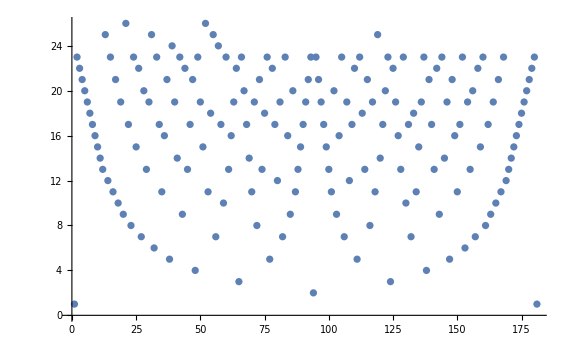

```mathematica
ListPlot[t]
```

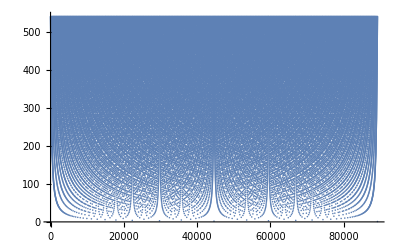

```mathematica
ListPlot[Denominator[FareySequence[p]]]
```

```mathematica
p
```

541

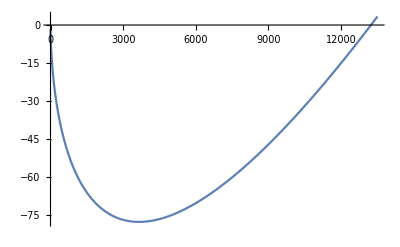

```mathematica
g[p_]:=(1/3-3/Pi^2)p-Sqrt[p](1+Log[p]/4)-2/3;
Plot[g[p],{p,1,13500}]
```

```mathematica
NSolve[g[t]==0&&t>0,Reals]
```

{{t→13231.8}}

```mathematica
PrimeQ[13219]
```

True

```mathematica
p=Prime[4];
S=Sum[EulerPhi[i],{i,1,Floor[Sqrt[p]]}];
Print[S];
For[j=5,j<=2500,j++,
p0=p;
p=Prime[j];
S+=Sum[EulerPhi[i],{i,Floor[Sqrt[p0]]+1,Floor[Sqrt[p]]}];
T=Floor[(p+1)/3];
Print["p = ",p];
If[S==T,Print["Compact at p = ",p]];
]
```

2

p = 11

Compact at p = 11

p = 13

Compact at p = 13

p = 17

Compact at p = 17

p = 19

Compact at p = 19

p = 23

p = 29

Compact at p = 29

p = 31

Compact at p = 31

p = 37

Compact at p = 37

p = 41

p = 43

p = 47

p = 53

Compact at p = 53

p = 59

p = 61

p = 67

Compact at p = 67

p = 71

p = 73

p = 79

p = 83

Compact at p = 83

p = 89

p = 97

p = 101

p = 103

p = 107

p = 109

p = 113

p = 127

Compact at p = 127

p = 131

p = 137

p = 139

p = 149

p = 151

p = 157

p = 163

p = 167

p = 173

Compact at p = 173

p = 179

p = 181

p = 191

p = 193

p = 197

p = 199

p = 211

p = 223

p = 227

p = 229

p = 233

p = 239

p = 241

p = 251

p = 257

p = 263

p = 269

p = 271

p = 277

p = 281

p = 283

p = 293

p = 307

p = 311

p = 313

p = 317

p = 331

p = 337

p = 347

p = 349

p = 353

p = 359

p = 367

p = 373

p = 379

p = 383

p = 389

p = 397

p = 401

p = 409

p = 419

p = 421

p = 431

p = 433

p = 439

p = 443

p = 449

p = 457

p = 461

p = 463

p = 467

p = 479

p = 487

p = 491

p = 499

p = 503

p = 509

p = 521

p = 523

p = 541

p = 547

p = 557

p = 563

p = 569

p = 571

p = 577

p = 587

p = 593

p = 599

p = 601

p = 607

p = 613

p = 617

p = 619

p = 631

p = 641

p = 643

p = 647

p = 653

p = 659

p = 661

p = 673

p = 677

p = 683

p = 691

p = 701

p = 709

p = 719

p = 727

p = 733

p = 739

p = 743

p = 751

p = 757

p = 761

p = 769

p = 773

p = 787

p = 797

p = 809

p = 811

p = 821

p = 823

p = 827

p = 829

p = 839

p = 853

p = 857

p = 859

p = 863

p = 877

p = 881

p = 883

p = 887

p = 907

p = 911

p = 919

p = 929

p = 937

p = 941

p = 947

p = 953

p = 967

p = 971

p = 977

p = 983

p = 991

p = 997

p = 1009

p = 1013

p = 1019

p = 1021

p = 1031

p = 1033

p = 1039

p = 1049

p = 1051

p = 1061

p = 1063

p = 1069

p = 1087

p = 1091

p = 1093

p = 1097

p = 1103

p = 1109

p = 1117

p = 1123

p = 1129

p = 1151

p = 1153

p = 1163

p = 1171

p = 1181

p = 1187

p = 1193

p = 1201

p = 1213

p = 1217

p = 1223

p = 1229

p = 1231

p = 1237

p = 1249

p = 1259

p = 1277

p = 1279

p = 1283

p = 1289

p = 1291

p = 1297

p = 1301

p = 1303

p = 1307

p = 1319

p = 1321

p = 1327

p = 1361

p = 1367

p = 1373

p = 1381

p = 1399

p = 1409

p = 1423

p = 1427

p = 1429

p = 1433

p = 1439

p = 1447

p = 1451

p = 1453

p = 1459

p = 1471

p = 1481

p = 1483

p = 1487

p = 1489

p = 1493

p = 1499

p = 1511

p = 1523

p = 1531

p = 1543

p = 1549

p = 1553

p = 1559

p = 1567

p = 1571

p = 1579

p = 1583

p = 1597

p = 1601

p = 1607

p = 1609

p = 1613

p = 1619

p = 1621

p = 1627

p = 1637

p = 1657

p = 1663

p = 1667

p = 1669

p = 1693

p = 1697

p = 1699

p = 1709

p = 1721

p = 1723

p = 1733

p = 1741

p = 1747

p = 1753

p = 1759

p = 1777

p = 1783

p = 1787

p = 1789

p = 1801

p = 1811

p = 1823

p = 1831

p = 1847

p = 1861

p = 1867

p = 1871

p = 1873

p = 1877

p = 1879

p = 1889

p = 1901

p = 1907

p = 1913

p = 1931

p = 1933

p = 1949

p = 1951

p = 1973

p = 1979

p = 1987

p = 1993

p = 1997

p = 1999

p = 2003

p = 2011

p = 2017

p = 2027

p = 2029

p = 2039

p = 2053

p = 2063

p = 2069

p = 2081

p = 2083

p = 2087

p = 2089

p = 2099

p = 2111

p = 2113

p = 2129

p = 2131

p = 2137

p = 2141

p = 2143

p = 2153

p = 2161

p = 2179

p = 2203

p = 2207

p = 2213

p = 2221

p = 2237

p = 2239

p = 2243

p = 2251

p = 2267

p = 2269

p = 2273

p = 2281

p = 2287

p = 2293

p = 2297

p = 2309

p = 2311

p = 2333

p = 2339

p = 2341

p = 2347

p = 2351

p = 2357

p = 2371

p = 2377

p = 2381

p = 2383

p = 2389

p = 2393

p = 2399

p = 2411

p = 2417

p = 2423

p = 2437

p = 2441

p = 2447

p = 2459

p = 2467

p = 2473

p = 2477

p = 2503

p = 2521

p = 2531

p = 2539

p = 2543

p = 2549

p = 2551

p = 2557

p = 2579

p = 2591

p = 2593

p = 2609

p = 2617

p = 2621

p = 2633

p = 2647

p = 2657

p = 2659

p = 2663

p = 2671

p = 2677

p = 2683

p = 2687

p = 2689

p = 2693

p = 2699

p = 2707

p = 2711

p = 2713

p = 2719

p = 2729

p = 2731

p = 2741

p = 2749

p = 2753

p = 2767

p = 2777

p = 2789

p = 2791

p = 2797

p = 2801

p = 2803

p = 2819

p = 2833

p = 2837

p = 2843

p = 2851

p = 2857

p = 2861

p = 2879

p = 2887

p = 2897

p = 2903

p = 2909

p = 2917

p = 2927

p = 2939

p = 2953

p = 2957

p = 2963

p = 2969

p = 2971

p = 2999

p = 3001

p = 3011

p = 3019

p = 3023

p = 3037

p = 3041

p = 3049

p = 3061

p = 3067

p = 3079

p = 3083

p = 3089

p = 3109

p = 3119

p = 3121

p = 3137

p = 3163

p = 3167

p = 3169

p = 3181

p = 3187

p = 3191

p = 3203

p = 3209

p = 3217

p = 3221

p = 3229

p = 3251

p = 3253

p = 3257

p = 3259

p = 3271

p = 3299

p = 3301

p = 3307

p = 3313

p = 3319

p = 3323

p = 3329

p = 3331

p = 3343

p = 3347

p = 3359

p = 3361

p = 3371

p = 3373

p = 3389

p = 3391

p = 3407

p = 3413

p = 3433

p = 3449

p = 3457

p = 3461

p = 3463

p = 3467

p = 3469

p = 3491

p = 3499

p = 3511

p = 3517

p = 3527

p = 3529

p = 3533

p = 3539

p = 3541

p = 3547

p = 3557

p = 3559

p = 3571

p = 3581

p = 3583

p = 3593

p = 3607

p = 3613

p = 3617

p = 3623

p = 3631

p = 3637

p = 3643

p = 3659

p = 3671

p = 3673

p = 3677

p = 3691

p = 3697

p = 3701

p = 3709

p = 3719

p = 3727

p = 3733

p = 3739

p = 3761

p = 3767

p = 3769

p = 3779

p = 3793

p = 3797

p = 3803

p = 3821

p = 3823

p = 3833

p = 3847

p = 3851

p = 3853

p = 3863

p = 3877

p = 3881

p = 3889

p = 3907

p = 3911

p = 3917

p = 3919

p = 3923

p = 3929

p = 3931

p = 3943

p = 3947

p = 3967

p = 3989

p = 4001

p = 4003

p = 4007

p = 4013

p = 4019

p = 4021

p = 4027

p = 4049

p = 4051

p = 4057

p = 4073

p = 4079

p = 4091

p = 4093

p = 4099

p = 4111

p = 4127

p = 4129

p = 4133

p = 4139

p = 4153

p = 4157

p = 4159

p = 4177

p = 4201

p = 4211

p = 4217

p = 4219

p = 4229

p = 4231

p = 4241

p = 4243

p = 4253

p = 4259

p = 4261

p = 4271

p = 4273

p = 4283

p = 4289

p = 4297

p = 4327

p = 4337

p = 4339

p = 4349

p = 4357

p = 4363

p = 4373

p = 4391

p = 4397

p = 4409

p = 4421

p = 4423

p = 4441

p = 4447

p = 4451

p = 4457

p = 4463

p = 4481

p = 4483

p = 4493

p = 4507

p = 4513

p = 4517

p = 4519

p = 4523

p = 4547

p = 4549

p = 4561

p = 4567

p = 4583

p = 4591

p = 4597

p = 4603

p = 4621

p = 4637

p = 4639

p = 4643

p = 4649

p = 4651

p = 4657

p = 4663

p = 4673

p = 4679

p = 4691

p = 4703

p = 4721

p = 4723

p = 4729

p = 4733

p = 4751

p = 4759

p = 4783

p = 4787

p = 4789

p = 4793

p = 4799

p = 4801

p = 4813

p = 4817

p = 4831

p = 4861

p = 4871

p = 4877

p = 4889

p = 4903

p = 4909

p = 4919

p = 4931

p = 4933

p = 4937

p = 4943

p = 4951

p = 4957

p = 4967

p = 4969

p = 4973

p = 4987

p = 4993

p = 4999

p = 5003

p = 5009

p = 5011

p = 5021

p = 5023

p = 5039

p = 5051

p = 5059

p = 5077

p = 5081

p = 5087

p = 5099

p = 5101

p = 5107

p = 5113

p = 5119

p = 5147

p = 5153

p = 5167

p = 5171

p = 5179

p = 5189

p = 5197

p = 5209

p = 5227

p = 5231

p = 5233

p = 5237

p = 5261

p = 5273

p = 5279

p = 5281

p = 5297

p = 5303

p = 5309

p = 5323

p = 5333

p = 5347

p = 5351

p = 5381

p = 5387

p = 5393

p = 5399

p = 5407

p = 5413

p = 5417

p = 5419

p = 5431

p = 5437

p = 5441

p = 5443

p = 5449

p = 5471

p = 5477

p = 5479

p = 5483

p = 5501

p = 5503

p = 5507

p = 5519

p = 5521

p = 5527

p = 5531

p = 5557

p = 5563

p = 5569

p = 5573

p = 5581

p = 5591

p = 5623

p = 5639

p = 5641

p = 5647

p = 5651

p = 5653

p = 5657

p = 5659

p = 5669

p = 5683

p = 5689

p = 5693

p = 5701

p = 5711

p = 5717

p = 5737

p = 5741

p = 5743

p = 5749

p = 5779

p = 5783

p = 5791

p = 5801

p = 5807

p = 5813

p = 5821

p = 5827

p = 5839

p = 5843

p = 5849

p = 5851

p = 5857

p = 5861

p = 5867

p = 5869

p = 5879

p = 5881

p = 5897

p = 5903

p = 5923

p = 5927

p = 5939

p = 5953

p = 5981

p = 5987

p = 6007

p = 6011

p = 6029

p = 6037

p = 6043

p = 6047

p = 6053

p = 6067

p = 6073

p = 6079

p = 6089

p = 6091

p = 6101

p = 6113

p = 6121

p = 6131

p = 6133

p = 6143

p = 6151

p = 6163

p = 6173

p = 6197

p = 6199

p = 6203

p = 6211

p = 6217

p = 6221

p = 6229

p = 6247

p = 6257

p = 6263

p = 6269

p = 6271

p = 6277

p = 6287

p = 6299

p = 6301

p = 6311

p = 6317

p = 6323

p = 6329

p = 6337

p = 6343

p = 6353

p = 6359

p = 6361

p = 6367

p = 6373

p = 6379

p = 6389

p = 6397

p = 6421

p = 6427

p = 6449

p = 6451

p = 6469

p = 6473

p = 6481

p = 6491

p = 6521

p = 6529

p = 6547

p = 6551

p = 6553

p = 6563

p = 6569

p = 6571

p = 6577

p = 6581

p = 6599

p = 6607

p = 6619

p = 6637

p = 6653

p = 6659

p = 6661

p = 6673

p = 6679

p = 6689

p = 6691

p = 6701

p = 6703

p = 6709

p = 6719

p = 6733

p = 6737

p = 6761

p = 6763

p = 6779

p = 6781

p = 6791

p = 6793

p = 6803

p = 6823

p = 6827

p = 6829

p = 6833

p = 6841

p = 6857

p = 6863

p = 6869

p = 6871

p = 6883

p = 6899

p = 6907

p = 6911

p = 6917

p = 6947

p = 6949

p = 6959

p = 6961

p = 6967

p = 6971

p = 6977

p = 6983

p = 6991

p = 6997

p = 7001

p = 7013

p = 7019

p = 7027

p = 7039

p = 7043

p = 7057

p = 7069

p = 7079

p = 7103

p = 7109

p = 7121

p = 7127

p = 7129

p = 7151

p = 7159

p = 7177

p = 7187

p = 7193

p = 7207

p = 7211

p = 7213

p = 7219

p = 7229

p = 7237

p = 7243

p = 7247

p = 7253

p = 7283

p = 7297

p = 7307

p = 7309

p = 7321

p = 7331

p = 7333

p = 7349

p = 7351

p = 7369

p = 7393

p = 7411

p = 7417

p = 7433

p = 7451

p = 7457

p = 7459

p = 7477

p = 7481

p = 7487

p = 7489

p = 7499

p = 7507

p = 7517

p = 7523

p = 7529

p = 7537

p = 7541

p = 7547

p = 7549

p = 7559

p = 7561

p = 7573

p = 7577

p = 7583

p = 7589

p = 7591

p = 7603

p = 7607

p = 7621

p = 7639

p = 7643

p = 7649

p = 7669

p = 7673

p = 7681

p = 7687

p = 7691

p = 7699

p = 7703

p = 7717

p = 7723

p = 7727

p = 7741

p = 7753

p = 7757

p = 7759

p = 7789

p = 7793

p = 7817

p = 7823

p = 7829

p = 7841

p = 7853

p = 7867

p = 7873

p = 7877

p = 7879

p = 7883

p = 7901

p = 7907

p = 7919

p = 7927

p = 7933

p = 7937

p = 7949

p = 7951

p = 7963

p = 7993

p = 8009

p = 8011

p = 8017

p = 8039

p = 8053

p = 8059

p = 8069

p = 8081

p = 8087

p = 8089

p = 8093

p = 8101

p = 8111

p = 8117

p = 8123

p = 8147

p = 8161

p = 8167

p = 8171

p = 8179

p = 8191

p = 8209

p = 8219

p = 8221

p = 8231

p = 8233

p = 8237

p = 8243

p = 8263

p = 8269

p = 8273

p = 8287

p = 8291

p = 8293

p = 8297

p = 8311

p = 8317

p = 8329

p = 8353

p = 8363

p = 8369

p = 8377

p = 8387

p = 8389

p = 8419

p = 8423

p = 8429

p = 8431

p = 8443

p = 8447

p = 8461

p = 8467

p = 8501

p = 8513

p = 8521

p = 8527

p = 8537

p = 8539

p = 8543

p = 8563

p = 8573

p = 8581

p = 8597

p = 8599

p = 8609

p = 8623

p = 8627

p = 8629

p = 8641

p = 8647

p = 8663

p = 8669

p = 8677

p = 8681

p = 8689

p = 8693

p = 8699

p = 8707

p = 8713

p = 8719

p = 8731

p = 8737

p = 8741

p = 8747

p = 8753

p = 8761

p = 8779

p = 8783

p = 8803

p = 8807

p = 8819

p = 8821

p = 8831

p = 8837

p = 8839

p = 8849

p = 8861

p = 8863

p = 8867

p = 8887

p = 8893

p = 8923

p = 8929

p = 8933

p = 8941

p = 8951

p = 8963

p = 8969

p = 8971

p = 8999

p = 9001

p = 9007

p = 9011

p = 9013

p = 9029

p = 9041

p = 9043

p = 9049

p = 9059

p = 9067

p = 9091

p = 9103

p = 9109

p = 9127

p = 9133

p = 9137

p = 9151

p = 9157

p = 9161

p = 9173

p = 9181

p = 9187

p = 9199

p = 9203

p = 9209

p = 9221

p = 9227

p = 9239

p = 9241

p = 9257

p = 9277

p = 9281

p = 9283

p = 9293

p = 9311

p = 9319

p = 9323

p = 9337

p = 9341

p = 9343

p = 9349

p = 9371

p = 9377

p = 9391

p = 9397

p = 9403

p = 9413

p = 9419

p = 9421

p = 9431

p = 9433

p = 9437

p = 9439

p = 9461

p = 9463

p = 9467

p = 9473

p = 9479

p = 9491

p = 9497

p = 9511

p = 9521

p = 9533

p = 9539

p = 9547

p = 9551

p = 9587

p = 9601

p = 9613

p = 9619

p = 9623

p = 9629

p = 9631

p = 9643

p = 9649

p = 9661

p = 9677

p = 9679

p = 9689

p = 9697

p = 9719

p = 9721

p = 9733

p = 9739

p = 9743

p = 9749

p = 9767

p = 9769

p = 9781

p = 9787

p = 9791

p = 9803

p = 9811

p = 9817

p = 9829

p = 9833

p = 9839

p = 9851

p = 9857

p = 9859

p = 9871

p = 9883

p = 9887

p = 9901

p = 9907

p = 9923

p = 9929

p = 9931

p = 9941

p = 9949

p = 9967

p = 9973

p = 10007

p = 10009

p = 10037

p = 10039

p = 10061

p = 10067

p = 10069

p = 10079

p = 10091

p = 10093

p = 10099

p = 10103

p = 10111

p = 10133

p = 10139

p = 10141

p = 10151

p = 10159

p = 10163

p = 10169

p = 10177

p = 10181

p = 10193

p = 10211

p = 10223

p = 10243

p = 10247

p = 10253

p = 10259

p = 10267

p = 10271

p = 10273

p = 10289

p = 10301

p = 10303

p = 10313

p = 10321

p = 10331

p = 10333

p = 10337

p = 10343

p = 10357

p = 10369

p = 10391

p = 10399

p = 10427

p = 10429

p = 10433

p = 10453

p = 10457

p = 10459

p = 10463

p = 10477

p = 10487

p = 10499

p = 10501

p = 10513

p = 10529

p = 10531

p = 10559

p = 10567

p = 10589

p = 10597

p = 10601

p = 10607

p = 10613

p = 10627

p = 10631

p = 10639

p = 10651

p = 10657

p = 10663

p = 10667

p = 10687

p = 10691

p = 10709

p = 10711

p = 10723

p = 10729

p = 10733

p = 10739

p = 10753

p = 10771

p = 10781

p = 10789

p = 10799

p = 10831

p = 10837

p = 10847

p = 10853

p = 10859

p = 10861

p = 10867

p = 10883

p = 10889

p = 10891

p = 10903

p = 10909

p = 10937

p = 10939

p = 10949

p = 10957

p = 10973

p = 10979

p = 10987

p = 10993

p = 11003

p = 11027

p = 11047

p = 11057

p = 11059

p = 11069

p = 11071

p = 11083

p = 11087

p = 11093

p = 11113

p = 11117

p = 11119

p = 11131

p = 11149

p = 11159

p = 11161

p = 11171

p = 11173

p = 11177

p = 11197

p = 11213

p = 11239

p = 11243

p = 11251

p = 11257

p = 11261

p = 11273

p = 11279

p = 11287

p = 11299

p = 11311

p = 11317

p = 11321

p = 11329

p = 11351

p = 11353

p = 11369

p = 11383

p = 11393

p = 11399

p = 11411

p = 11423

p = 11437

p = 11443

p = 11447

p = 11467

p = 11471

p = 11483

p = 11489

p = 11491

p = 11497

p = 11503

p = 11519

p = 11527

p = 11549

p = 11551

p = 11579

p = 11587

p = 11593

p = 11597

p = 11617

p = 11621

p = 11633

p = 11657

p = 11677

p = 11681

p = 11689

p = 11699

p = 11701

p = 11717

p = 11719

p = 11731

p = 11743

p = 11777

p = 11779

p = 11783

p = 11789

p = 11801

p = 11807

p = 11813

p = 11821

p = 11827

p = 11831

p = 11833

p = 11839

p = 11863

p = 11867

p = 11887

p = 11897

p = 11903

p = 11909

p = 11923

p = 11927

p = 11933

p = 11939

p = 11941

p = 11953

p = 11959

p = 11969

p = 11971

p = 11981

p = 11987

p = 12007

p = 12011

p = 12037

p = 12041

p = 12043

p = 12049

p = 12071

p = 12073

p = 12097

p = 12101

p = 12107

p = 12109

p = 12113

p = 12119

p = 12143

p = 12149

p = 12157

p = 12161

p = 12163

p = 12197

p = 12203

p = 12211

p = 12227

p = 12239

p = 12241

p = 12251

p = 12253

p = 12263

p = 12269

p = 12277

p = 12281

p = 12289

p = 12301

p = 12323

p = 12329

p = 12343

p = 12347

p = 12373

p = 12377

p = 12379

p = 12391

p = 12401

p = 12409

p = 12413

p = 12421

p = 12433

p = 12437

p = 12451

p = 12457

p = 12473

p = 12479

p = 12487

p = 12491

p = 12497

p = 12503

p = 12511

p = 12517

p = 12527

p = 12539

p = 12541

p = 12547

p = 12553

p = 12569

p = 12577

p = 12583

p = 12589

p = 12601

p = 12611

p = 12613

p = 12619

p = 12637

p = 12641

p = 12647

p = 12653

p = 12659

p = 12671

p = 12689

p = 12697

p = 12703

p = 12713

p = 12721

p = 12739

p = 12743

p = 12757

p = 12763

p = 12781

p = 12791

p = 12799

p = 12809

p = 12821

p = 12823

p = 12829

p = 12841

p = 12853

p = 12889

p = 12893

p = 12899

p = 12907

p = 12911

p = 12917

p = 12919

p = 12923

p = 12941

p = 12953

p = 12959

p = 12967

p = 12973

p = 12979

p = 12983

p = 13001

p = 13003

p = 13007

p = 13009

p = 13033

p = 13037

p = 13043

p = 13049

p = 13063

p = 13093

p = 13099

p = 13103

p = 13109

p = 13121

p = 13127

p = 13147

p = 13151

p = 13159

p = 13163

p = 13171

p = 13177

p = 13183

p = 13187

p = 13217

p = 13219

p = 13229

p = 13241

p = 13249

p = 13259

p = 13267

p = 13291

p = 13297

p = 13309

p = 13313

p = 13327

p = 13331

p = 13337

p = 13339

p = 13367

p = 13381

p = 13397

p = 13399

p = 13411

p = 13417

p = 13421

p = 13441

p = 13451

p = 13457

p = 13463

p = 13469

p = 13477

p = 13487

p = 13499

p = 13513

p = 13523

p = 13537

p = 13553

p = 13567

p = 13577

p = 13591

p = 13597

p = 13613

p = 13619

p = 13627

p = 13633

p = 13649

p = 13669

p = 13679

p = 13681

p = 13687

p = 13691

p = 13693

p = 13697

p = 13709

p = 13711

p = 13721

p = 13723

p = 13729

p = 13751

p = 13757

p = 13759

p = 13763

p = 13781

p = 13789

p = 13799

p = 13807

p = 13829

p = 13831

p = 13841

p = 13859

p = 13873

p = 13877

p = 13879

p = 13883

p = 13901

p = 13903

p = 13907

p = 13913

p = 13921

p = 13931

p = 13933

p = 13963

p = 13967

p = 13997

p = 13999

p = 14009

p = 14011

p = 14029

p = 14033

p = 14051

p = 14057

p = 14071

p = 14081

p = 14083

p = 14087

p = 14107

p = 14143

p = 14149

p = 14153

p = 14159

p = 14173

p = 14177

p = 14197

p = 14207

p = 14221

p = 14243

p = 14249

p = 14251

p = 14281

p = 14293

p = 14303

p = 14321

p = 14323

p = 14327

p = 14341

p = 14347

p = 14369

p = 14387

p = 14389

p = 14401

p = 14407

p = 14411

p = 14419

p = 14423

p = 14431

p = 14437

p = 14447

p = 14449

p = 14461

p = 14479

p = 14489

p = 14503

p = 14519

p = 14533

p = 14537

p = 14543

p = 14549

p = 14551

p = 14557

p = 14561

p = 14563

p = 14591

p = 14593

p = 14621

p = 14627

p = 14629

p = 14633

p = 14639

p = 14653

p = 14657

p = 14669

p = 14683

p = 14699

p = 14713

p = 14717

p = 14723

p = 14731

p = 14737

p = 14741

p = 14747

p = 14753

p = 14759

p = 14767

p = 14771

p = 14779

p = 14783

p = 14797

p = 14813

p = 14821

p = 14827

p = 14831

p = 14843

p = 14851

p = 14867

p = 14869

p = 14879

p = 14887

p = 14891

p = 14897

p = 14923

p = 14929

p = 14939

p = 14947

p = 14951

p = 14957

p = 14969

p = 14983

p = 15013

p = 15017

p = 15031

p = 15053

p = 15061

p = 15073

p = 15077

p = 15083

p = 15091

p = 15101

p = 15107

p = 15121

p = 15131

p = 15137

p = 15139

p = 15149

p = 15161

p = 15173

p = 15187

p = 15193

p = 15199

p = 15217

p = 15227

p = 15233

p = 15241

p = 15259

p = 15263

p = 15269

p = 15271

p = 15277

p = 15287

p = 15289

p = 15299

p = 15307

p = 15313

p = 15319

p = 15329

p = 15331

p = 15349

p = 15359

p = 15361

p = 15373

p = 15377

p = 15383

p = 15391

p = 15401

p = 15413

p = 15427

p = 15439

p = 15443

p = 15451

p = 15461

p = 15467

p = 15473

p = 15493

p = 15497

p = 15511

p = 15527

p = 15541

p = 15551

p = 15559

p = 15569

p = 15581

p = 15583

p = 15601

p = 15607

p = 15619

p = 15629

p = 15641

p = 15643

p = 15647

p = 15649

p = 15661

p = 15667

p = 15671

p = 15679

p = 15683

p = 15727

p = 15731

p = 15733

p = 15737

p = 15739

p = 15749

p = 15761

p = 15767

p = 15773

p = 15787

p = 15791

p = 15797

p = 15803

p = 15809

p = 15817

p = 15823

p = 15859

p = 15877

p = 15881

p = 15887

p = 15889

p = 15901

p = 15907

p = 15913

p = 15919

p = 15923

p = 15937

p = 15959

p = 15971

p = 15973

p = 15991

p = 16001

p = 16007

p = 16033

p = 16057

p = 16061

p = 16063

p = 16067

p = 16069

p = 16073

p = 16087

p = 16091

p = 16097

p = 16103

p = 16111

p = 16127

p = 16139

p = 16141

p = 16183

p = 16187

p = 16189

p = 16193

p = 16217

p = 16223

p = 16229

p = 16231

p = 16249

p = 16253

p = 16267

p = 16273

p = 16301

p = 16319

p = 16333

p = 16339

p = 16349

p = 16361

p = 16363

p = 16369

p = 16381

p = 16411

p = 16417

p = 16421

p = 16427

p = 16433

p = 16447

p = 16451

p = 16453

p = 16477

p = 16481

p = 16487

p = 16493

p = 16519

p = 16529

p = 16547

p = 16553

p = 16561

p = 16567

p = 16573

p = 16603

p = 16607

p = 16619

p = 16631

p = 16633

p = 16649

p = 16651

p = 16657

p = 16661

p = 16673

p = 16691

p = 16693

p = 16699

p = 16703

p = 16729

p = 16741

p = 16747

p = 16759

p = 16763

p = 16787

p = 16811

p = 16823

p = 16829

p = 16831

p = 16843

p = 16871

p = 16879

p = 16883

p = 16889

p = 16901

p = 16903

p = 16921

p = 16927

p = 16931

p = 16937

p = 16943

p = 16963

p = 16979

p = 16981

p = 16987

p = 16993

p = 17011

p = 17021

p = 17027

p = 17029

p = 17033

p = 17041

p = 17047

p = 17053

p = 17077

p = 17093

p = 17099

p = 17107

p = 17117

p = 17123

p = 17137

p = 17159

p = 17167

p = 17183

p = 17189

p = 17191

p = 17203

p = 17207

p = 17209

p = 17231

p = 17239

p = 17257

p = 17291

p = 17293

p = 17299

p = 17317

p = 17321

p = 17327

p = 17333

p = 17341

p = 17351

p = 17359

p = 17377

p = 17383

p = 17387

p = 17389

p = 17393

p = 17401

p = 17417

p = 17419

p = 17431

p = 17443

p = 17449

p = 17467

p = 17471

p = 17477

p = 17483

p = 17489

p = 17491

p = 17497

p = 17509

p = 17519

p = 17539

p = 17551

p = 17569

p = 17573

p = 17579

p = 17581

p = 17597

p = 17599

p = 17609

p = 17623

p = 17627

p = 17657

p = 17659

p = 17669

p = 17681

p = 17683

p = 17707

p = 17713

p = 17729

p = 17737

p = 17747

p = 17749

p = 17761

p = 17783

p = 17789

p = 17791

p = 17807

p = 17827

p = 17837

p = 17839

p = 17851

p = 17863

p = 17881

p = 17891

p = 17903

p = 17909

p = 17911

p = 17921

p = 17923

p = 17929

p = 17939

p = 17957

p = 17959

p = 17971

p = 17977

p = 17981

p = 17987

p = 17989

p = 18013

p = 18041

p = 18043

p = 18047

p = 18049

p = 18059

p = 18061

p = 18077

p = 18089

p = 18097

p = 18119

p = 18121

p = 18127

p = 18131

p = 18133

p = 18143

p = 18149

p = 18169

p = 18181

p = 18191

p = 18199

p = 18211

p = 18217

p = 18223

p = 18229

p = 18233

p = 18251

p = 18253

p = 18257

p = 18269

p = 18287

p = 18289

p = 18301

p = 18307

p = 18311

p = 18313

p = 18329

p = 18341

p = 18353

p = 18367

p = 18371

p = 18379

p = 18397

p = 18401

p = 18413

p = 18427

p = 18433

p = 18439

p = 18443

p = 18451

p = 18457

p = 18461

p = 18481

p = 18493

p = 18503

p = 18517

p = 18521

p = 18523

p = 18539

p = 18541

p = 18553

p = 18583

p = 18587

p = 18593

p = 18617

p = 18637

p = 18661

p = 18671

p = 18679

p = 18691

p = 18701

p = 18713

p = 18719

p = 18731

p = 18743

p = 18749

p = 18757

p = 18773

p = 18787

p = 18793

p = 18797

p = 18803

p = 18839

p = 18859

p = 18869

p = 18899

p = 18911

p = 18913

p = 18917

p = 18919

p = 18947

p = 18959

p = 18973

p = 18979

p = 19001

p = 19009

p = 19013

p = 19031

p = 19037

p = 19051

p = 19069

p = 19073

p = 19079

p = 19081

p = 19087

p = 19121

p = 19139

p = 19141

p = 19157

p = 19163

p = 19181

p = 19183

p = 19207

p = 19211

p = 19213

p = 19219

p = 19231

p = 19237

p = 19249

p = 19259

p = 19267

p = 19273

p = 19289

p = 19301

p = 19309

p = 19319

p = 19333

p = 19373

p = 19379

p = 19381

p = 19387

p = 19391

p = 19403

p = 19417

p = 19421

p = 19423

p = 19427

p = 19429

p = 19433

p = 19441

p = 19447

p = 19457

p = 19463

p = 19469

p = 19471

p = 19477

p = 19483

p = 19489

p = 19501

p = 19507

p = 19531

p = 19541

p = 19543

p = 19553

p = 19559

p = 19571

p = 19577

p = 19583

p = 19597

p = 19603

p = 19609

p = 19661

p = 19681

p = 19687

p = 19697

p = 19699

p = 19709

p = 19717

p = 19727

p = 19739

p = 19751

p = 19753

p = 19759

p = 19763

p = 19777

p = 19793

p = 19801

p = 19813

p = 19819

p = 19841

p = 19843

p = 19853

p = 19861

p = 19867

p = 19889

p = 19891

p = 19913

p = 19919

p = 19927

p = 19937

p = 19949

p = 19961

p = 19963

p = 19973

p = 19979

p = 19991

p = 19993

p = 19997

p = 20011

p = 20021

p = 20023

p = 20029

p = 20047

p = 20051

p = 20063

p = 20071

p = 20089

p = 20101

p = 20107

p = 20113

p = 20117

p = 20123

p = 20129

p = 20143

p = 20147

p = 20149

p = 20161

p = 20173

p = 20177

p = 20183

p = 20201

p = 20219

p = 20231

p = 20233

p = 20249

p = 20261

p = 20269

p = 20287

p = 20297

p = 20323

p = 20327

p = 20333

p = 20341

p = 20347

p = 20353

p = 20357

p = 20359

p = 20369

p = 20389

p = 20393

p = 20399

p = 20407

p = 20411

p = 20431

p = 20441

p = 20443

p = 20477

p = 20479

p = 20483

p = 20507

p = 20509

p = 20521

p = 20533

p = 20543

p = 20549

p = 20551

p = 20563

p = 20593

p = 20599

p = 20611

p = 20627

p = 20639

p = 20641

p = 20663

p = 20681

p = 20693

p = 20707

p = 20717

p = 20719

p = 20731

p = 20743

p = 20747

p = 20749

p = 20753

p = 20759

p = 20771

p = 20773

p = 20789

p = 20807

p = 20809

p = 20849

p = 20857

p = 20873

p = 20879

p = 20887

p = 20897

p = 20899

p = 20903

p = 20921

p = 20929

p = 20939

p = 20947

p = 20959

p = 20963

p = 20981

p = 20983

p = 21001

p = 21011

p = 21013

p = 21017

p = 21019

p = 21023

p = 21031

p = 21059

p = 21061

p = 21067

p = 21089

p = 21101

p = 21107

p = 21121

p = 21139

p = 21143

p = 21149

p = 21157

p = 21163

p = 21169

p = 21179

p = 21187

p = 21191

p = 21193

p = 21211

p = 21221

p = 21227

p = 21247

p = 21269

p = 21277

p = 21283

p = 21313

p = 21317

p = 21319

p = 21323

p = 21341

p = 21347

p = 21377

p = 21379

p = 21383

p = 21391

p = 21397

p = 21401

p = 21407

p = 21419

p = 21433

p = 21467

p = 21481

p = 21487

p = 21491

p = 21493

p = 21499

p = 21503

p = 21517

p = 21521

p = 21523

p = 21529

p = 21557

p = 21559

p = 21563

p = 21569

p = 21577

p = 21587

p = 21589

p = 21599

p = 21601

p = 21611

p = 21613

p = 21617

p = 21647

p = 21649

p = 21661

p = 21673

p = 21683

p = 21701

p = 21713

p = 21727

p = 21737

p = 21739

p = 21751

p = 21757

p = 21767

p = 21773

p = 21787

p = 21799

p = 21803

p = 21817

p = 21821

p = 21839

p = 21841

p = 21851

p = 21859

p = 21863

p = 21871

p = 21881

p = 21893

p = 21911

p = 21929

p = 21937

p = 21943

p = 21961

p = 21977

p = 21991

p = 21997

p = 22003

p = 22013

p = 22027

p = 22031

p = 22037

p = 22039

p = 22051

p = 22063

p = 22067

p = 22073

p = 22079

p = 22091

p = 22093

p = 22109

p = 22111

p = 22123

p = 22129

p = 22133

p = 22147

p = 22153

p = 22157

p = 22159

p = 22171

p = 22189

p = 22193

p = 22229

p = 22247

p = 22259

p = 22271

p = 22273

p = 22277

p = 22279

p = 22283

p = 22291

p = 22303

p = 22307

```mathematica
EulerPhi[1]
```

1

```mathematica
EulerPhi[2]
```

1

```mathematica
p
```

7

```mathematica
Prime[1000]
```

7919